Now, we look at the 2 degree of freedom quantum expander from Mikhail’s paper. He only states the input-output relation for one quadrature but we can find the other from the condition on G

```mathematica
SetDirectory[NotebookDirectory[]];
<<Simba`;
$Assumptions={γ>0,χ>0,ωs>0};
umat=1/(√2)({{1, 1}, {-ⅈ, ⅈ}});
```

```mathematica
(* NB: just guessed this, in future need to solve for G *)
transferMatrix={{((γ-χ)ω+ⅈ (ω^2-ωs^2))/((γ+χ)ω-ⅈ (ω^2-ωs^2)),0},{0,((γ+χ)ω+ⅈ (ω^2-ωs^2))/((γ-χ)ω-ⅈ (ω^2-ωs^2))}};
SymplecticΘ[transferMatrix/.ω->-ⅈ s,s]==ΘMatrix[1]//Simplify
transferMatrixSb=Inverse[umat].transferMatrix.umat//Simplify;
```

True

```mathematica
ssUnrealisable=MinimalStateSpaceModel@StateSpaceModel[TransferFunctionModel[-transferMatrix/.ω->-ⅈ s/.s->-s,s]]//Simplify
```

010000-ωs^2-γ-χ001000010000-ωs^2-γ+χ010-2 γ0010000-2 γ01StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2241FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Module[{umat2={{umat†,0},{0,umat†}}//ArrayFlatten,a,b,c,d},
{a,b,c,d}=Normal[ssUnrealisable];
ss=StateSpaceModel[{umat2†.a.umat2,umat2†.b.umat,umat†.c.umat2,d}]//Simplify]
```

1/2 (1-γ-χ-ωs^2)1/2 ⅈ (-1+γ+χ-ωs^2)001/21/2-1/2 ⅈ (1+γ+χ+ωs^2)1/2 (-1-γ-χ+ωs^2)00ⅈ/2ⅈ/2001/2 (1-γ+χ-ωs^2)1/2 ⅈ (-1+γ-χ-ωs^2)-ⅈ/2ⅈ/200-1/2 ⅈ (1+γ-χ+ωs^2)1/2 (-1-γ+χ+ωs^2)1/2-1/2-γⅈ γ-ⅈ γ-γ10-γⅈ γⅈ γγ01StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2241FalseFalseFalseAutomaticNoneAutomatic

```mathematica
{A==Part[#,1],B==Part[#,2],C==Part[#,3],D==Part[#,4]}&@Normal[ss]//TeXForm;
```

```mathematica
TransferFunctionModel[ss][-ⅈ ω]==-transferMatrixSb//Simplify
```

True

```mathematica
ObservableModelQ[ss]&&ControllableModelQ[ss]
```

True

Will find physically realisable state-space from Mikhail’s paper and infer X

a_q is SRC mode
a is arm mode

Equations of motion:
a_out=-a_in+√(2 γ)a_q
(ȧ)_q=-ⅈ ω_s a-χ a_q†-γ a_q+√(2 γ)a_in
ȧ=-ⅈ ω_s a_q

```mathematica
dynamical=({{0, 0, -ⅈ ωs / (-s), 0, 0, 0, 0, 0}, {0, 0, 0, ⅈ ωs / (-s), 0, 0, 0, 0}, {-ⅈ ωs / (-s), 0, -γ / (-s), -χ/(-s), √(2 γ) / (-s), 0, 0, 0}, {0, ⅈ ωs / (-s), -χ/(-s), -γ / (-s), 0, √(2 γ) / (-s), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, √(2 γ), 0, -1, 0, 0, 0}, {0, 0, 0, √(2 γ), 0, -1, 0, 0}});
Module[{states=First/@PositionIndex[{a,ad,aq,aqd,ain,aind,aout,aoutd}],
excitation=IdentityMatrix[8],tfm},
tfm=Inverse[excitation-dynamical];
Simplify[umat.{{tfm[[states[aout],states[ain]]], tfm[[states[aout],states[aind]]]},
{tfm[[states[aoutd],states[ain]]], tfm[[states[aoutd],states[aind]]]}}.Inverse[umat]]/.s->ⅈ ω]
```

{{-(ⅈ (γ-χ) ω-ω^2+ωs^2)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0},{0,-(ⅈ (γ+χ) ω-ω^2+ωs^2)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)}}

```mathematica
{{-(ⅈ (γ-χ) ω-ω^2+ωs^2)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0},{0,-(ⅈ (γ+χ) ω-ω^2+ωs^2)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)}}==transferMatrix//Simplify
```

True

```mathematica
Module[{a,b,c,d},
a=({{0, 0, -ⅈ ωs, 0}, {0, 0, 0, ⅈ ωs}, {-ⅈ ωs, 0, -γ, -χ}, {0, ⅈ ωs, -χ, -γ}});
b=({{0, 0}, {0, 0}, {√(2 γ), 0}, {0, √(2γ)}});
c=-({{0, 0, √(2 γ), 0}, {0, 0, 0, √(2 γ)}});
d=IdentityMatrix[2];
ssPhysical=StateSpaceModel[{a,b,c,d}]];
(umat.TransferFunctionModel[ssPhysical][-ⅈ ω].Inverse[umat]//Simplify)==-transferMatrix//Simplify
RealisableQ[ssPhysical]
```

True

True

```mathematica
tmat=Array[t,{4,4}];
Module[{a,b,c,d,ap,bp,cp,dp},
{a,b,c,d}=Normal[ss];
{ap,bp,cp,dp}=Normal[ssPhysical];
tmat=tmat/.
First[Solve[tmat.ap==a.tmat&&cp==c.tmat&&tmat.bp==b&&d==dp,Flatten[tmat]]//Simplify];
xmat=tmat.JMatrix[2].tmat†//Simplify]
```

{{0,0,(ⅈ (1+ωs^2))/(4 γ ωs^2),(-1+ωs^2)/(4 γ ωs^2)},{0,0,-(-1+ωs^2)/(4 γ ωs^2),(ⅈ (1+ωs^2))/(4 γ ωs^2)},{-(ⅈ (1+ωs^2))/(4 γ ωs^2),-(-1+ωs^2)/(4 γ ωs^2),0,0},{(-1+ωs^2)/(4 γ ωs^2),-(ⅈ (1+ωs^2))/(4 γ ωs^2),0,0}}

```mathematica
4 γ ωs^2 xmat/.ωs->Subscript[ω, s]//TeXForm
```

\left(
\begin{array}{cccc}
 0 & 0 & i \left(\omega _s^2+1\right) & \omega _s^2-1 \\
 0 & 0 & 1-\omega _s^2 & i \left(\omega _s^2+1\right) \\
 -i \left(\omega _s^2+1\right) & 1-\omega _s^2 & 0 & 0 \\
 \omega _s^2-1 & -i \left(\omega _s^2+1\right) & 0 & 0 \\
\end{array}
\right)

```mathematica
StateSpaceTransform[ss,tmat]==ssPhysical//Simplify
```

True

```mathematica
{A==Part[#,1],B==Part[#,2],C==Part[#,3],D==Part[#,4]}&@Normal[ssPhysical/.ωs->Subscript[ω, s]]//TeXForm;
```

```mathematica
Module[{states=First/@PositionIndex[{a,ad,aq,aqd,ain,aind,aout,aoutd}],
excitation=IdentityMatrix[8],tfm},
tfm=Inverse[excitation-dynamical];
Simplify[umat.{{tfm[[states[a],states[ain]]], tfm[[states[a],states[aind]]]},
{tfm[[states[ad],states[ain]]], tfm[[states[ad],states[aind]]]}}.Inverse[umat]]/.s->ⅈ ω]
```

{{0,(√2 √γ ωs)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)},{-(√2 √γ ωs)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0}}

```mathematica
Limit[{{0,(√2 √γ ωs)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)},{-(√2 √γ ωs)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0}},χ->γ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{{0,(√2 √γ ωs)/(-ω^2+ωs^2)},{-(√2 √γ ωs)/(-2 ⅈ γ ω-ω^2+ωs^2),0}}

```mathematica
{{0,(√2 √γ ωs)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)},{-(√2 √γ ωs)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0}}/.ωs->Subscript[ω, s]//TeXForm
```

\left(
\begin{array}{cc}
 0 & \frac{\sqrt{2} \sqrt{\gamma } \omega _s}{i \omega  (\chi -\gamma )+\omega
   _s^2-\omega ^2} \\
 -\frac{\sqrt{2} \sqrt{\gamma } \omega _s}{-i \omega  (\gamma +\chi )+\omega
   _s^2-\omega ^2} & 0 \\
\end{array}
\right)

Coupling of input phase quadrature fluctuations into amplitude quadrature diverges (∞ response), so we should ideally couple the signal to the amplitude quadrature in the arm in this limit

```mathematica
$Assumptions={γ>ωs,γ>0,ωs>0};
```

```mathematica
Solve[-2 ⅈ γ ω-ω^2+ωs^2==0,ω]//ComplexExpand//Simplify
```

{{ω→-ⅈ (γ+√(γ^2-ωs^2))},{ω→ⅈ (-γ+√(γ^2-ωs^2))}}

```mathematica
Solve[2 ⅈ γ ω-ω^2+ωs^2==0,ω]//ComplexExpand//Simplify
```

{{ω→ⅈ (γ-√(γ^2-ωs^2))},{ω→ⅈ (γ+√(γ^2-ωs^2))}}

```mathematica
γ-√(γ^2-ωs^2)>0//Simplify
```

True

Two positive imaginary roots at ω = ⅈ (γ-√(γ^2-ωs^2)) and ⅈ (γ+√(γ^2-ωs^2))

```mathematica
Module[{tf=Abs[-(√2 √γ ωs)/(-2 ⅈ γ ω-ω^2+ωs^2)]^2//ComplexExpand},
2 π ⅈ(Residue[tf,{ω,ⅈ (γ-√(γ^2-ωs^2))}]+Residue[tf,{ω,ⅈ (γ+√(γ^2-ωs^2))}])//Simplify]
```

π

non-threshold case for arm

```mathematica
$Assumptions={-γ^2+2 γ χ-χ^2+4 ωs^2>0,γ>ωs,γ>0,ωs>0,χ>0};
{{0,(√2 √γ ωs)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)},{-(√2 √γ ωs)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0}};
```

```mathematica
Simplify@*ReIm/@Join[ω/.Solve[ⅈ (-γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify,
ω/.Solve[-ⅈ (-γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify]
```

{{-1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),1/2 (-γ+χ)},{1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),1/2 (-γ+χ)},{-1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),(γ-χ)/2},{1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),(γ-χ)/2}}

Let’s assume γ > χ so that the latter two poles are in the upper half plane (makes no difference anyway apart from a minus sign as the real parts are degenerate)

```mathematica
Simplify[2 π ⅈ Module[{tf=Abs[(√2 √γ ωs)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)]^2//ComplexExpand},Residue[tf,{ω,-1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2)+ⅈ(γ-χ)/2}]+Residue[tf,{ω,1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2)+ⅈ(γ-χ)/2}]]]
```

(2 π γ)/(γ-χ)

```mathematica
Reduce[(2 γ)/(γ-χ)>1,γ]
```

(χ≤0&&(γ<χ||γ>-χ))||(χ>0&&(γ<-χ||γ>χ))

```mathematica
(2 π γ)/(γ-χ)
```

(2 π γ)/(γ-χ)

```mathematica
$Assumptions={-γ^2-2 γ χ-χ^2+4 ωs^2>0,γ>ωs,γ>0,ωs>0,χ>0};
Refine@*Simplify@*ReIm/@Join[ω/.Solve[-ⅈ (γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify,
ω/.Solve[ⅈ (γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify]
```

{{-1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),1/2 (-γ-χ)},{1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),1/2 (-γ-χ)},{1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),(γ+χ)/2},{-1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),(γ+χ)/2}}

```mathematica
Simplify[2 π ⅈ Module[{tf=Abs[-(√2 √γ ωs)/(-ⅈ (γ+χ) ω-ω^2+ωs^2)]^2//ComplexExpand},Residue[tf,{ω,1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2)+ⅈ(γ+χ)/2}]+Residue[tf,{ω,-1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2)+ⅈ(γ+χ)/2}]]]
```

(2 π γ)/(γ+χ)

```mathematica
Module[{states=First/@PositionIndex[{a,ad,aq,aqd,ain,aind,aout,aoutd}],
excitation=IdentityMatrix[8],tfm},
tfm=Inverse[excitation-dynamical];
Simplify[umat.{{tfm[[states[aq],states[ain]]], tfm[[states[aq],states[aind]]]},
{tfm[[states[aqd],states[ain]]], tfm[[states[aqd],states[aind]]]}}.Inverse[umat]]/.s->ⅈ ω]
```

{{-(ⅈ √2 √γ ω)/(-ⅈ (γ+χ) ω-ω^2+ωs^2),0},{0,-(ⅈ √2 √γ ω)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)}}

```mathematica
$Assumptions={-γ^2-2 γ χ-χ^2+4 ωs^2>0,γ>ωs,γ>0,ωs>0,χ>0};
Refine@*Simplify@*ReIm/@Join[ω/.Solve[-ⅈ (γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify,
ω/.Solve[ⅈ (γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify]
```

{{-1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),1/2 (-γ-χ)},{1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),1/2 (-γ-χ)},{1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),(γ+χ)/2},{-1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2),(γ+χ)/2}}

```mathematica
Simplify[2 π ⅈ Module[{tf=Abs[-(ⅈ √2 √γ ω)/(-ⅈ (γ+χ) ω-ω^2+ωs^2)]^2//ComplexExpand},Residue[tf,{ω,-1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2)+ⅈ(γ+χ)/2}]+Residue[tf,{ω,1/2 √(-γ^2-2 γ χ-χ^2+4 ωs^2)+ⅈ(γ+χ)/2}]]]
```

(2 π γ)/(γ+χ)

```mathematica
$Assumptions={-γ^2-2 γ χ-χ^2+4 ωs^2>0,γ>ωs,γ>0,ωs>0,χ>0};
Refine@*Simplify@*ReIm/@Join[ω/.Solve[ⅈ (-γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify,
ω/.Solve[-ⅈ (-γ+χ) ω-ω^2+ωs^2==0,ω]//Simplify]
```

{{-1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),1/2 (-γ+χ)},{1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),1/2 (-γ+χ)},{-1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),(γ-χ)/2},{1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2),(γ-χ)/2}}

```mathematica
Simplify[2 π ⅈ Module[{tf=Abs[-(ⅈ √2 √γ ω)/(ⅈ (-γ+χ) ω-ω^2+ωs^2)]^2//ComplexExpand},Residue[tf,{ω,-1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2)+ⅈ(γ-χ)/2}]+Residue[tf,{ω,1/2 √(-γ^2+2 γ χ-χ^2+4 ωs^2)+ⅈ(γ-χ)/2}]]]
```

(2 π γ)/(γ-χ)

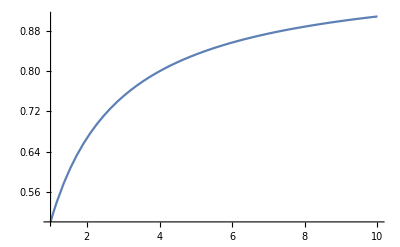

```mathematica
Plot[1/(1+1/x),{x,1,10}]
```

```mathematica
Maximize[(2 π γ)/Abs[γ+χ]//ComplexExpand,χ]
```

{Piecewise[{{∞, γ>0}, {0, True}}],{χ→Piecewise[{{-1, γ==0}, {Indeterminate, True}}]}}